# Procesamiento Digital de Imagenes Práctica 1 “MTF del ojo humano” Dr. Boris Escalante R. Guzmán Villanueva Julio César Marmolejo Servín Genaro Floriano Pérez Humberto

Realizar el cálculo necesario para obtener la función sinuosidal modulada en frecuencia y en amplitud (cálculo
de las constantes).

Asumiendo que la frecuencia evaluada en el pixel 512 vale ℼ y la frecuencia evaluada en el pixel 0 es 0.0137; se establecen las siguientes ecuaciones.

```mathematica
f:=0.0137;
k2 = Log[π/f]/512;
k1 = f/k2;
```

De las ecuaciones anteriores, los valores de k1 y k2 son:

```mathematica
k1
```

1.29058

```mathematica
k2
```

0.0106154

Se propone el parametro z1 para detener la atenuación vertical a  3/4 partes de la imagen de 512×512 pixeles

```mathematica
z1=3/4*512;
```

Con los valores de k1, k2 y z1 se plantean las siguientes ecuaciones.

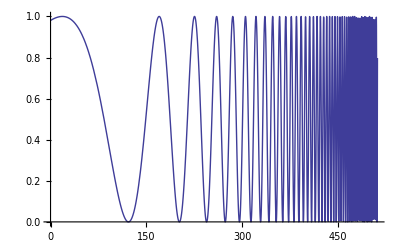

```mathematica
Plot[1/2*Sin[k1*ⅇ^(k2*x)]+1/2,{x,0,512}]
```

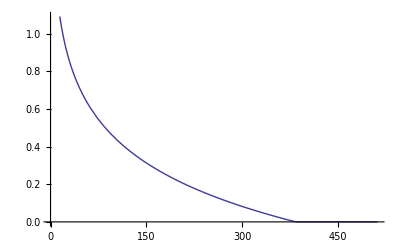

```mathematica
Plot[(-Log[y/z1]+ Log[y/z1] * UnitStep[y-z1]  )/3,{y,0,512}]
```

A partir de las dos funciones anteriores se construye la siguiente ecuación.

```mathematica
Plot3D[((1/2*Sin[k1*ⅇ^(k2*x)]*(-Log[y/z1]/3+ Log[y/z1]/3 * UnitStep[y-z1]  ))+1/2),{x,0,512},{y,0,512}]
```

-Graphics3D-

Construyendo la imagen a partir de la ecuación anterior.

```mathematica
imagen = Image[Table[((1/2*Sin[k1*ⅇ^(k2*x)]*(-Log[y/z1]/3.5 + Log[y/z1]/3.5 * UnitStep[y-z1] ))+1/2),{y,512,0,-.9},{x,0,512,.9} ]]
```

-Graphics-

Posteriormente exportamos la imagen para las mediciones correspondientes.

```mathematica
Export["Frecuencia.gif", imagen]
```

Calculando la frecuencia de máxima sensibilidad ( en Ciclos/grado ) a 3 distancias diferentes de observación.

Genaro Marmolejo

```mathematica
pixel:=306;
distanciapixel:= .17/512;
distancia:= .88;

c =  (k1 * k2 * ⅇ^(k2 * pixel))/(2π);
α = ArcTan[distanciapixel/distancia];
ciclosporgrado:= c/α * π/180;
ciclosporgrado
```

2.59685

```mathematica
pixel:=259;
distanciapixel:= .17/512;
distancia:= 1.76;

c =  (k1 * k2 * ⅇ^(k2 * pixel))/(2π);
α = ArcTan[distanciapixel/distancia];
ciclosporgrado:= c/α * π/180;
ciclosporgrado
```

3.15353

```mathematica
pixel:= 168;
distanciapixel:= 0.17/512;
distancia:= 2.64;

c =  (k1 * k2 * ⅇ^(k2 * pixel))/(2π);
α = ArcTan[distanciapixel/distancia];
ciclosporgrado:= c/α * π/180;
ciclosporgrado
```

1.80036

Humberto Floriano

```mathematica
pixel:=454;
distanciapixel:= .15/512;
distancia:= 1;

c =  (k1 * k2 * ⅇ^(k2 * pixel))/(2π);
α = ArcTan[distanciapixel/distancia];
ciclosporgrado:= c/α * π/180;
ciclosporgrado
```

16.0929

```mathematica
pixel:=382;
distanciapixel:= .15/512;
distancia:= 2;

c =  (k1 * k2 * ⅇ^(k2 * pixel))/(2π);
α = ArcTan[distanciapixel/distancia];
ciclosporgrado:= c/α * π/180;
ciclosporgrado
```

14.9875

```mathematica
pixel:= 358;
distanciapixel:= 0.15/512;
distancia:= 3;

c =  (k1 * k2 * ⅇ^(k2 * pixel))/(2π);
α = ArcTan[distanciapixel/distancia];
ciclosporgrado:= c/α * π/180;
ciclosporgrado
```

17.4251

Julio César Guzmán

```mathematica
pixel:= 295;
distanciapixel:= .178/512;
distancia:= 1;

c =  (k1 * k2 * ⅇ^(k2 * pixel))/(2π);
α = ArcTan[distanciapixel/distancia];
ciclosporgrado:= c/α * π/180;
ciclosporgrado
```

2.50773

```mathematica
pixel:=295;
distanciapixel:= .178/512;
distancia:= 2;

c =  (k1 * k2 * ⅇ^(k2 * pixel))/(2π);
α = ArcTan[distanciapixel/distancia];
ciclosporgrado:= c/α * π/180;
ciclosporgrado
```

5.01546

```mathematica
pixel:= 266;
distanciapixel:= 0.178/512;
distancia:= 3;

c =  (k1 * k2 * ⅇ^(k2 * pixel))/(2π);
α = ArcTan[distanciapixel/distancia];
ciclosporgrado:= c/α * π/180;
ciclosporgrado
```

5.52976

## Conclusión

En esta practica pudimos comprobar la frecuencia de máxima sensibilidad del sistema de visión humano de los participantes, usando un estimulo visual que consistía en una senoidal modulada cuya frecuencia variaba conforme a una exponencial. 
Una vez calculadas las funciones, se desplegaron en pantalla y se hicieron mediciones a tres distancias diferentes. Con esos puntos se realizaron los cálculos necesarios para convertir las medidas de pixeles en ciclos por grado.
Dentro de los problemas encontrados primero fue la generación de la excitación visual, concretamente, encontrar las funciones para generar la MFT de tal manera que en la parte superior se desplegara un color diferente al negro absoluto, es decir el cambio de contraste.
Otro de los problemas es el grado de variación en los resultados de los integrantes del equipo, esto puede deberse a que la frecuencia de máxima sensibilidad varia de una persona a otra y/o a un error asociado a la medición junto con  la diferencia de contraste y de nivel de profundidad de colores, de los diferentes monitores usados por los integrantes.